# Lab3 Appendix C: Angular Velocity Decay

## Initialization

General assumptions when solving equations

```mathematica
$Assumptions= R>0 ∧ 0≤ϕ≤2π ∧ 0≤θ≤π ∧ 0≤β≤π ∧
ρ>0 ∧ m>0 ∧ C𝒟≥0 ∧ n > 0 ∧vb > 0 ∧
vx∈Reals∧ vy∈Reals ∧ vz∈Reals ∧ ωx> 0 ∧ ωy> 0 ∧ ωz> 0;
```

Definition of the vector norm symbol

```mathematica
|v_|:=√(v_⟦1⟧^2+v_⟦2⟧^2+v_⟦3⟧^2)
```

## Equations

Velocity of the surface element δA at position r relative to the fluid is

```mathematica
𝒰:=v+ω×r
```

where v is velocity of the ball throught the fluid and ω is angular velocity of the ball.

Let us assume that an infinitesimal drag force at the surface element δA is

```mathematica
δf:=-1/2 ρ C𝒟 δA  (|𝒰|)^(γ-1)𝒰
```

where ρ is mass density of the fluid, C_D is a constant that depends on the surface material, and γ characterizes type of the flow (γ = 1 for laminar flow and γ = 2 for turbulent flow).

An infinitesimal torque caused by the drag force is then

```mathematica
δτ:=r×δf
```

where the net torque is τ=∫δτ integrated across the surface.

Angular acceleration of the ball can be expressed from the net torque as

```mathematica
ω̇:=ℐ^-1 τ
```

where ℐ is the moment of inertia of the ball (i.e. sphere)

```mathematica
ℐ:=2/5 m R^2
```

## Parameters

Taking as a parameter ball cross section area A

```mathematica
A:=π R^2
```

together with a constant C_𝓌 that depends on type of surface and moment of inertia

```mathematica
C𝓌:=20/3 C𝒟
```

and introducing constant of proportionality k_𝓌

```mathematica
k𝓌:=1/2 (ρ A C𝓌)/m
```

```mathematica
k𝓌
```

(10 C𝒟 π R^2 ρ)/(3 m)

## Coordinate System

#### Spherical Coordinates

Position of the surface element δA in in spherical coordinates is

```mathematica
r:={
R Cos[ϕ]Sin[θ],
R Sin[ϕ]Sin[θ],
R Cos[θ]
}
```

The area of the surface element is

```mathematica
δA:=R^2 δΩ
```

where δΩ is an infinitesimal solid angle subtended  by the surface element, in spherical coordinates expressed as

```mathematica
δΩ:=Sin[θ]δθ δϕ
```

Velocity of the ball throught the fluid v in cartesian coordinates

```mathematica
v:={vx,vy,vz}
```

Angular velocity ω of the ball in cartesian coordinates

```mathematica
ω:={ωx,ωy,ωz}
```

Velocity of the surface element relative to the fluid in cartesian coordinates

```mathematica
{{"𝓊_x =","𝓊_y =","𝓊_z ="},𝒰}//Transpose//TableForm
```

𝓊_x = | vx+R ωy Cos[θ]-R ωz Sin[θ] Sin[ϕ]
𝓊_y = | vy-R ωx Cos[θ]+R ωz Cos[ϕ] Sin[θ]
𝓊_z = | vz-R ωy Cos[ϕ] Sin[θ]+R ωx Sin[θ] Sin[ϕ]

#### Sanity-Check

Verify that the ball surface area is ∫δA=4π R^2

```mathematica
∫_0^π ∫_0^(2π) (δA/(δθ δϕ))ⅆϕ ⅆθ==4 π R^2
```

True

## Solving Equations

Let's find angular acceleration α=τ/(k_𝓌 ℐ) by integrationg the net torque τ=∫δτ across the whole surface.

#### Laminar Flow

```mathematica
γ=1;θ=.;ϕ=.;
v={vx,vy,vz};
ω={ωx,ωy,ωz};
```

```mathematica
δα[γ]=δτ/(ℐ δθ δϕ)//FullSimplify;
```

```mathematica
α[γ]=∫_0^π ∫_0^(2π) δα[γ]ⅆϕ ⅆθ;
```

```mathematica
{{"(ω̇)_x =","(ω̇)_y =","(ω̇)_z ="},α[γ]}//Transpose//TableForm
```

(ω̇)_x = | -(10 C𝒟 π R^2 ρ ωx)/(3 m)
(ω̇)_y = | -(10 C𝒟 π R^2 ρ ωy)/(3 m)
(ω̇)_z = | -(10 C𝒟 π R^2 ρ ωz)/(3 m)

```mathematica
Solve[{αx,αy,αz}==α[γ]&&Subscript[k, 𝓌]==1/2 (ρ A C𝓌)/m,{αx,αy,αz}][[1]]//TableForm
```

αx→-ωx k_𝓌
αy→-ωy k_𝓌
αz→-ωz k_𝓌

Conclusion:

α==-k_w  ω

#### Turbulent Flow, ω = 0

```mathematica
γ=2;θ=.;ϕ=.;
v={vx,vy,vz};
ω={0,0,0};
```

```mathematica
δα[γ]=δτ/(ℐ δθ δϕ)//FullSimplify;
```

```mathematica
α[γ]=∫_0^π ∫_0^(2π) δα[γ]ⅆϕ ⅆθ;
```

```mathematica
{{"(ω̇)_x =","(ω̇)_y =","(ω̇)_z ="},α[γ]}//Transpose//TableForm
```

(ω̇)_x = | 0
(ω̇)_y = | 0
(ω̇)_z = | 0

```mathematica
Solve[{αx,αy,αz}==α[γ]&&Subscript[k, 𝓌]==1/2 (ρ A C𝓌)/m,{αx,αy,αz}][[1]]//TableForm
```

αx→0
αy→0
αz→0

Conclusion:

α==0  for  ω==0

#### Turbulent Flow, v = 0

```mathematica
γ=2;θ=.;ϕ=.;
v={0,0,0};
ω={0,0,ωz};
```

```mathematica
δα[γ]=δτ/(ℐ δθ δϕ)//FullSimplify;
```

```mathematica
α[γ]=∫_0^π ∫_0^(2π) δα[γ]ⅆϕ ⅆθ;
```

```mathematica
{{"(ω̇)_x =","(ω̇)_y =","(ω̇)_z ="},α[γ]}//Transpose//TableForm
```

(ω̇)_x = | 0
(ω̇)_y = | 0
(ω̇)_z = | -(15 C𝒟 π^2 R^3 ρ ωz^2)/(16 m)

```mathematica
Solve[{αx,αy,αz}==α[γ]&&Subscript[k, 𝓌]==1/2 (ρ A C𝓌)/m,{αx,αy,αz}][[1]]//TableForm
```

αx→0
αy→0
αz→-9/32 π R ωz^2 k_𝓌

Conclusion:

α_z==-k_w ω_z |R ω_z| for v==0.

#### Turbulent Flow, vx ≠ 0, ωz ≠ 0, θ == π/2

```mathematica
γ=2;θ=π/2;ϕ=.;R=.;
v={vx,0,0};
ω={0,0,ωz};
```

```mathematica
δα[γ]=δτ/(Subscript[k, 𝓌] ℐδθ δϕ)//FullSimplify
```

{0,0,(3 (-R ωz+vx Sin[ϕ]) √(vx^2+R^2 ωz^2-2 R vx ωz Sin[ϕ]))/(8 π R)}

```mathematica
α3=∫δα[γ]_⟦3⟧ⅆϕ//FullSimplify
```

(-2 R vx ωz Cos[ϕ] (vx^2+R^2 ωz^2-2 R vx ωz Sin[ϕ])+(vx-R ωz)^2 ((vx^2+7 R^2 ωz^2) EllipticE[1/4 (π-2 ϕ),-(4 R vx ωz)/(vx-R ωz)^2]-(vx+R ωz)^2 EllipticF[1/4 (π-2 ϕ),-(4 R vx ωz)/(vx-R ωz)^2]) √((vx^2+R^2 ωz^2-2 R vx ωz Sin[ϕ])/(vx-R ωz)^2))/(8 π R^2 ωz √(vx^2+R^2 ωz^2-2 R vx ωz Sin[ϕ]))

```mathematica
(α3/.ϕ->2π)-(α3/.ϕ->0)//FullSimplify
```

-1/(8 π R^2 ωz)Abs[vx-R ωz] ((vx^2+7 R^2 ωz^2) EllipticE[π/4,-(4 R vx ωz)/(vx-R ωz)^2]+(vx^2+7 R^2 ωz^2) EllipticE[(3 π)/4,-(4 R vx ωz)/(vx-R ωz)^2]-(vx+R ωz)^2 (EllipticF[π/4,-(4 R vx ωz)/(vx-R ωz)^2]+EllipticF[(3 π)/4,-(4 R vx ωz)/(vx-R ωz)^2]))

Continued with manual simplification...

```mathematica
γ=2;θ=π/2;ϕ=.;R=.;
v={vx,0,0};
ω={0,0,ωz};
vx=.;ωz=.;
```

```mathematica
E1E:=EllipticE[ π/4,-(4 R vx ωz)/(vx-R ωz)^2 ]+EllipticE[ (3π)/4,-(4 R vx ωz)/(vx-R ωz)^2 ];
```

```mathematica
E1F:=EllipticF[ π/4,-(4 R vx ωz)/(vx-R ωz)^2 ]+EllipticF[ (3π)/4,-(4 R vx ωz)/(vx-R ωz)^2 ];
```

```mathematica
E3:=-Abs[vx-R ωz]/(8 π R^2 ωz) ((vx^2+7 R^2 ωz^2)E1E-(vx+R ωz)^2 E1F)
```

```mathematica
E3:=-Abs[vx-R ωz]/(8 π) ωz(((vx/(R ωz))^2+7)E1E-(vx/(R ωz)+1)^2 E1F)
```

```mathematica
Limit[ E3,vx->0,Assumptions->ωz∈Reals∧R>0]
```

-3/4 R ωz Abs[ωz]

```mathematica
Limit[ E3,ωz->0]
```

0

```mathematica
ωz=1;vx=-1.001;R=1;E3//N
```

-1.27419

```mathematica
ωz=1;vx=-10^6;R=1;E3//N
```

-1.12498×10^6

```mathematica
ωz=1;vx=-10^7;R=1;E3//N
```

-1.12652×10^7

```mathematica
ωz=10^4;vx=-1;R=1;E3//N
```

-7.5×10^7

```mathematica
ωz=10^5;vx=-1;R=1;E3//N
```

-7.5×10^9

```mathematica
ωz=1;vx=-1.001;R=10^8;E3//N
```

-7.5×10^7

```mathematica
ωz=1;vx=-1.001;R=10^9;E3//N
```

-7.5×10^8

There exists:
	1) square dependence of angular velocity, 
	2) linear dependence of linear velocity, and 
	3) linear dependence on radius.

Conclusion:

α_z∝-k_w ω_z (|v_x|+|R ω_z|)

#### Turbulent Flow, golf ball, numerical analysis

```mathematica
γ=2;θ=.;ϕ=.;
ρ=1.3;m=0.045;R=0.02;Subscript[C, 𝒟]=1;Subscript[C, 𝓌]=10;
ωz=.;vx=.;
v:={vx,0,0}
ω:={0,0,ωz}
```

Numerical solution

```mathematica
δα[γ]=δτ/(ℐ δθ δϕ)//FullSimplify;
```

```mathematica
foo[vx_,ωz_]=δα[γ][[3]];
```

```mathematica
sol[vx_,ωz_]:=NIntegrate[foo[vx,ωz],{ϕ,0,2π},{θ,0,π}]
```

Guessed solution

```mathematica
guessed[vx_,ωz_]:=-1/2 (ρ A Subscript[C, 𝓌])/m ωz( R ωz+vx)
```

Comparison of numerical solution (top diagram) and guessed solution (bottom diagram) where abscissa = v_x and ordinate = ω̇

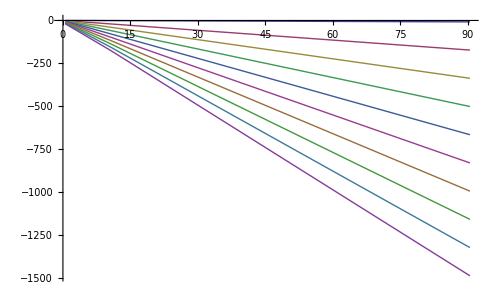

```mathematica
ListLinePlot[Table[Table[{vx,sol[vx,ωz]},{vx,0.5,100,10}],{ωz,0.5,100,10}]]
```

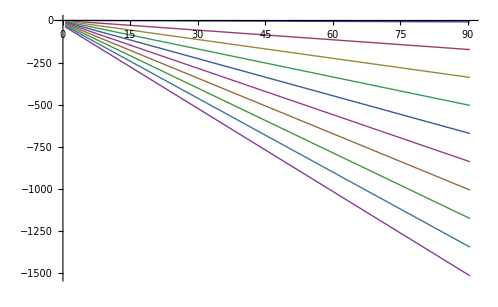

```mathematica
ListLinePlot[Table[Table[{vx,guessed[vx,ωz]},{vx,0.5,100,10}],{ωz,0.5,100,10}]]
```

Comparison of numerical solution (top diagram) and guessed solution (bottom diagram) where abscissa = ω_z and ordinate = ω̇

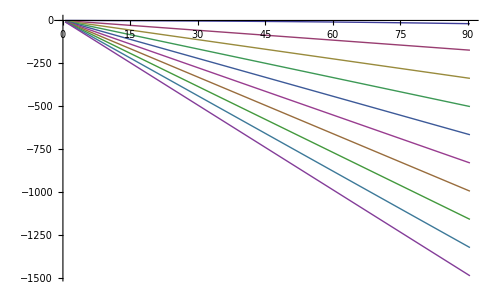

```mathematica
ListLinePlot[Table[Table[{ωz,sol[vx,ωz]},{ωz,0.5,100,10}],{vx,0.5,100,10}]]
```

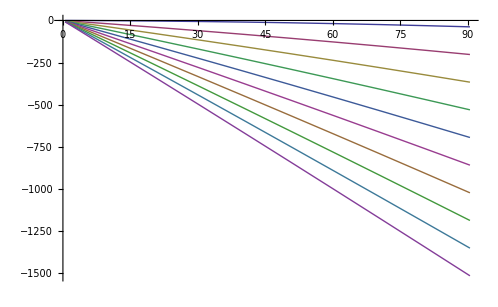

```mathematica
ListLinePlot[Table[Table[{ωz,guessed[vx,ωz]},{ωz,0.5,100,10}],{vx,0.5,100,10}]]
```

#### Turbulent Flow, vx ≠ 0, ωz ≠ 0, θ == π/2

```mathematica
γ=2;θ=.;ϕ=.;
β=.;R=.;ρ=.;C𝒟=.;m=.;
ωz=.; n=.;
```

Let us take coordinate with z-axis along ω

```mathematica
ω:={0,0,ωz}
```

and that the ball velocity is parametrized by the intensity ratio n to ω and the departuring angle β from ω

```mathematica
v:={vb Sin[β],0,vb Cos[β]}
```

so the velocity of the surface element is

```mathematica
{{"𝓊_x =","𝓊_y =","𝓊_z ="},𝒰}//FullSimplify//Transpose//TableForm
```

𝓊_x = | vb Sin[β]-R ωz Sin[θ] Sin[ϕ]
𝓊_y = | R ωz Cos[ϕ] Sin[θ]
𝓊_z = | vb Cos[β]

Then the infinitesimal torque on the surface element is

```mathematica
n:=vb/(R ωz);n=.;
```

```mathematica
k:=5/4(ρ C𝒟 R^3)/m;k=.;
```

```mathematica
δα[γ,ωz_,n_,β_,k_]:=k ωz^2 Sin[θ]^2 √(Sin[θ]^2+n^2-2 n Sin[β] Sin[θ] Sin[ϕ])×
{
Cos[θ] Cos[ϕ]-n Cos[β] Sin[ϕ],
n Cos[β] Cos[ϕ]-n Cot[θ] Sin[β]+Cos[θ] Sin[ϕ],
-Sin[θ]+n Sin[β] Sin[ϕ]
}
```

```mathematica
δα2[γ]=δτ/(ℐ δθ δϕ)//TrigReduce//FullSimplify;
```

```mathematica
{{"δα_x =","δα_y =","δα_z ="},δα2[γ]}//Transpose//TableForm
```

δα_x = | (5 C𝒟 R ρ Sin[θ]^2 (R ωz Cos[θ] Cos[ϕ]-vb Cos[β] Sin[ϕ]) √(4 vb^2+2 R^2 ωz^2-2 R ωz (R ωz Cos[2 θ]+4 vb Sin[β] Sin[θ] Sin[ϕ])))/(8 m)
δα_y = | (5 C𝒟 R ρ Sin[θ] (vb Cos[β] Cos[ϕ] Sin[θ]+Cos[θ] (-vb Sin[β]+R ωz Sin[θ] Sin[ϕ])) √(4 vb^2+2 R^2 ωz^2-2 R ωz (R ωz Cos[2 θ]+4 vb Sin[β] Sin[θ] Sin[ϕ])))/(8 m)
δα_z = | (5 C𝒟 R ρ Sin[θ]^2 (-R ωz Sin[θ]+vb Sin[β] Sin[ϕ]) √(4 vb^2+2 R^2 ωz^2-2 R ωz (R ωz Cos[2 θ]+4 vb Sin[β] Sin[θ] Sin[ϕ])))/(8 m)

```mathematica
δα[γ,ωz,vb/(R ωz),β,5/4(ρ C𝒟 R^3)/m]==δα2[γ]//FullSimplify
```

True

```mathematica
∫_0^π ∫_0^(2π) δα[γ,ωz,0,0,k R^2]ⅆϕⅆθ
```

{0,0,-3/4 k π^2 R^2 ωz^2}

```mathematica
∫_0^π ∫_0^(2π) δα[γ,0,n,β,k R^2]ⅆϕⅆθ
```

{0,0,0}

```mathematica
∫_0^π ∫_0^(2π) δα[γ,ωz,n,0,k R^2]ⅆϕⅆθ
```

{0,0,-1/2 k π R^2 ωz^2 (n (3+n^2)+(3+2 n^2-n^4) ArcCot[n])}

```mathematica
-1/2 k π R^2 ωz^2 (n (3+n^2))/.n->vb/(R ωz)//FullSimplify
```

```mathematica
-1/2 k π  vb (3 R^2 ωz^2+vb^2)/(R ωz)
```

```mathematica
∫_0^(2π) δα[γ,1,1,π/2,k R^2]ⅆϕ
```

$Aborted

```mathematica
f1[ωz_,n_]=Normal[Series[δα[γ,ωz,n,π/2,1]//Expand,{ϕ,0,15},{θ,0,15}]]//N;
```

```mathematica
f2[ωz_,n_]=f1[ωz,n]//Expand;
```

```mathematica
f3[ωz_,n_]=∫_0^π ∫_0^(2π) f2[ωz,n]ⅆϕⅆθ//N;
```

```mathematica
f4[ωz_,n_]=f3[ωz,n]//Expand;
```

```mathematica
f4[1,1]//Expand
```

{2.33876×10^21,1.49128×10^20,-1.72368×10^20}

```mathematica
f1=Normal[Series[δα[γ,1,1,π/2,1]//Expand,{ϕ,0,100},{θ,0,100}]]//N;
```

$Aborted

```mathematica
∫_0^π ∫_0^(2π) f1 ⅆϕⅆθ//N;
```

```mathematica
f4[ωz_,n_]=f3[ωz,n]//Expand;
```

```mathematica
f4[1,1]//Expand
```

{2.33876×10^21,1.49128×10^20,-1.72368×10^20}

where we need to calculate

```mathematica
∫_0^π ∫_0^(2π) δα[γ]ⅆϕⅆθ
```

which we will do by developing δα into series.

```mathematica
β=1;R=1;ρ=1;C𝒟=1;m=1;
```

```mathematica
N$s=15;
```

Series of δα[γ]

```mathematica
serϕ[ϕ_]=Normal[Series[δα[γ],{ϕ,0,N$s}]];
```

Indefinite integral of series of δα[γ] of ϕ

```mathematica
intϕ[ϕ_]=Module[{t},(∫serϕ[t]ⅆt)/.t->ϕ];
```

Series of definite integral ∫_0^(2 π) δα(γ)ⅆϕ of θ

```mathematica
detintϕ[θ_]=intϕ[2π]-intϕ[0];
```

```mathematica
serθ[θ_]=Normal[Series[detintϕ[θ],{θ,0,N$s}]];
```

$Aborted

Indefinite integral of series of ∫_0^(2 π) δα(γ)ⅆϕ of θ

```mathematica
intθ[θ_]=Module[{t},(∫serθ[t]ⅆt)/.t->θ];
```

The solution is definite integral ∫_0^π ∫_0^(2π) δα[γ]ⅆϕⅆθ

The last integral is the solution:

```mathematica
solution=intθ[π]-intθ[0]//TrigFactor;
```

The last integral is the solution:

```mathematica
solution[0.0001,π/2,1,1,1,1,1]//TableForm//N
```

1.00543×10^41
1.41282×10^40
-2.11923×10^36

```mathematica
detintθ[0.00001,0]
```

{-7.6286×10^10 R^5 ρ ωz^2 C_𝒟,-3.7841×10^10 R^5 ρ ωz^2 C_𝒟,1.70409×10^7 R^5 ρ ωz^2 C_𝒟}

```mathematica
intϕ[2π]-intϕ[0]
```

$Aborted[]

```mathematica
(1 - Cos[2 θ])/2//FullSimplify
```

Sin[θ]^2

```mathematica
1/2+1/2 Cos[2 θ]//FullSimplify
```

Cos[θ]^2

```mathematica
(1-Cos[2 θ])/2
```

```mathematica
1/2 (1-Cos[2 θ])//FullSimplify
```

Sin[θ]^2

```mathematica
2×3
```

6

```mathematica
∫√(1+0.3 Sin[x])ⅆx
```

$Aborted

```mathematica
∫Normal[Series[Sqrt[1+0.5Sin[x]],{x,0,15}]]ⅆx
```

x+0.125 x^2-0.0104167 x^3-0.00846354 x^4+0.00159505 x^5-0.000161404 x^6-0.0000116742 x^7+0.0000263199 x^8-0.000013309 x^9+4.21711×10^-6 x^10-6.34074×10^-7 x^11-2.2985×10^-7 x^12+2.35009×10^-7 x^13-1.08655×10^-7 x^14+2.97933×10^-8 x^15-7.45211×10^-10 x^16